## Functions

```mathematica
flattening[assoc_]:=Map[Flatten,Apply[List,Normal[assoc],{1}]]
```

```mathematica
arrangingFunction[a_]:=Module[{b,f},b=Subsets[Range[Length[a]],{2}];
f=Function[Nearest[#->Range[Length[#]]]][Map[Function[Apply[EuclideanDistance,a[[#]]]],b]];
b[[f[3.14,Length[a]/2]]]]
```

```mathematica
distance[a_,b_]:=EuclideanDistance[positions[[a]],positions[[b]]]
```

## Image Processing

```mathematica
importImage=Import["C:\\Users\\DELL\\Desktop\\graph.png"]
```

-Graphics-

```mathematica
binarizedImage=Binarize[importImage]
```

-Graphics-

```mathematica
Grid[{{"importImage","binarizedImage",""},{importImage,binarizedImage,l}},Frame->All]//Magnify
```

importImage | binarizedImage | 
-Graphics- | -Graphics- | l

```mathematica
detectedVertices=SelectComponents[binarizedImage,"Count",Function[5<#<100]]
```

-Graphics-

```mathematica
verticesCoordinates=ComponentMeasurements[detectedVertices,"Centroid"]
```

{1→{149.,429.5},2→{324.,418.5},3→{551.,309.5},4→{314.,303.5},5→{11.,275.5},6→{214.914,210.534},7→{682.,182.5},8→{527.,109.5},9→{104.,64.5},10→{362.,13.5}}

```mathematica
detectedEdges=DeleteSmallComponents[ImageSubtract[Thinning[ColorNegate[binarizedImage]],Dilation[detectedVertices,10]],2]
```

-Graphics-

```mathematica
Grid[{{"detectedVertices","detectedEdges",""},{detectedVertices,detectedEdges,l}},Frame->All]//Magnify
```

detectedVertices | detectedEdges | 
-Graphics- | -Graphics- | l

```mathematica
separatedEdges=Map[Composition[Binarize,Image],Values[ComponentMeasurements[detectedEdges,"Mask"]]];
```

```mathematica
detectedCrosses=Select[separatedEdges,Function[ImageMeasurements[MorphologicalBranchPoints[#],"Total"]>1]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
detectedNonOverlapEdges=Complement[separatedEdges,detectedCrosses]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
nonOverlapEdgesEndpointsCoordinates=Map[Function[PixelValuePositions[#,1]],MorphologicalTransform[detectedNonOverlapEdges,"EndPoints"]]
```

{{{514,100},{376,22}},{{669,176},{541,113}},{{222,197},{351,27}},{{204,197},{116,78}},{{16,262},{95,79}},{{565,298},{670,195}},{{538,311},{328,304}},{{155,416},{211,225}},{{137,417},{23,289}}}

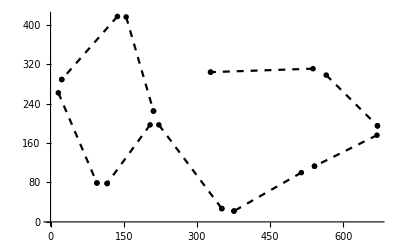

```mathematica
ListLinePlot[nonOverlapEdgesEndpointsCoordinates,PlotStyle->Dashed,PlotTheme->"Monochrome"]
```

```mathematica
separatedCrossesAtCenter=MapThread[ImageSubtract,{detectedCrosses,Map[Function[Dilation[MorphologicalBranchPoints[#],3]],detectedCrosses]}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
separatedCrosses=Map[Function[Map[Composition[Binarize,Image],Values[ComponentMeasurements[#,"Mask"]]]],separatedCrossesAtCenter]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
crossesCenterPointsCoordinates=MapThread[Function[Nearest[PixelValuePositions[MorphologicalTransform[#1,"EndPoints"],1],Mean[PixelValuePositions[MorphologicalBranchPoints[#2],1]],4]],{separatedCrossesAtCenter,detectedCrosses}]
```

{{{125,235},{120,241},{127,245},{130,238}},{{274,336},{281,338},{276,328},{283,329}},{{538,195},{537,187},{533,191},{542,191}}}

```mathematica
separatedCrossesEndpointsCoordinates=Table[Map[Function[PixelValuePositions[#,1]],Map[Function[MorphologicalTransform[#,"EndPoints"]],i]],{i,separatedCrosses}]
```

{{{{148,416},{127,245}},{{25,272},{120,241}},{{130,238},{202,214}},{{125,235},{106,79}}},{{{163,423},{274,336}},{{316,405},{281,338}},{{283,329},{301,315}},{{276,328},{223,225}}},{{{550,296},{538,195}},{{229,208},{533,191}},{{542,191},{669,183}},{{537,187},{529,124}}}}

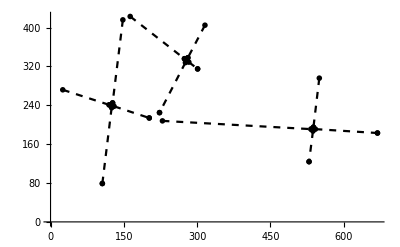

```mathematica
ListLinePlot[Flatten[separatedCrossesEndpointsCoordinates,1],PlotStyle->Dashed,PlotTheme->"Monochrome"]
```

```mathematica
unarrangedCrossesEndpointsCoordinates=MapThread[Function[{a,b},Catenate[MapThread[Complement,{Catenate[Map[Function[Select[a,MemberQ[#]]],b]],Map[List,b]}]]],{separatedCrossesEndpointsCoordinates,crossesCenterPointsCoordinates}]
```

{{{106,79},{25,272},{148,416},{202,214}},{{163,423},{316,405},{223,225},{301,315}},{{550,296},{529,124},{229,208},{669,183}}}

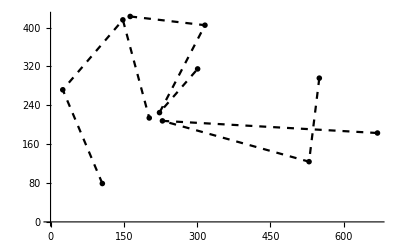

```mathematica
ListLinePlot[unarrangedCrossesEndpointsCoordinates,PlotStyle->Dashed,PlotTheme->"Monochrome"]
```

```mathematica
crossesEndpointsConnections=MapThread[Function[arrangingFunction[Table[Apply[ArcTan,PixelValuePositions[Image[MorphologicalComponents[#1]],PixelValue[Image[MorphologicalComponents[#1]],i]];
N[Mean[Select[PixelValuePositions[Image[MorphologicalComponents[#1]],PixelValue[Image[MorphologicalComponents[#1]],i]],Function[Norm[#-i]<20]]]]-i],{i,#2}]]],{separatedCrossesAtCenter,unarrangedCrossesEndpointsCoordinates}]
```

{{{1,3},{2,4}},{{2,3},{1,4}},{{1,2},{3,4}}}

```mathematica
crossesEndpointsCoordinates=MapThread[Function[Map[Function[i,Part[#1,i]],#2]],{unarrangedCrossesEndpointsCoordinates,crossesEndpointsConnections}]
```

{{{{106,79},{148,416}},{{25,272},{202,214}}},{{{316,405},{223,225}},{{163,423},{301,315}}},{{{550,296},{529,124}},{{229,208},{669,183}}}}

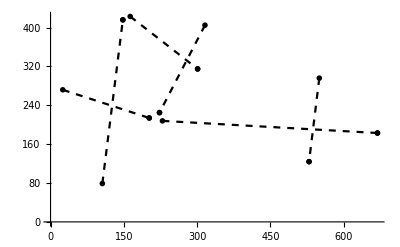

```mathematica
ListLinePlot[Flatten[crossesEndpointsCoordinates,1],PlotStyle->Dashed,PlotTheme->"Monochrome"]
```

```mathematica
edgesEndpointsCoordinates=Fold[Function[Join[#1,#2]],nonOverlapEdgesEndpointsCoordinates,crossesEndpointsCoordinates]
```

{{{514,100},{376,22}},{{669,176},{541,113}},{{222,197},{351,27}},{{204,197},{116,78}},{{16,262},{95,79}},{{565,298},{670,195}},{{538,311},{328,304}},{{155,416},{211,225}},{{137,417},{23,289}},{{106,79},{148,416}},{{25,272},{202,214}},{{316,405},{223,225}},{{163,423},{301,315}},{{550,296},{529,124}},{{229,208},{669,183}}}

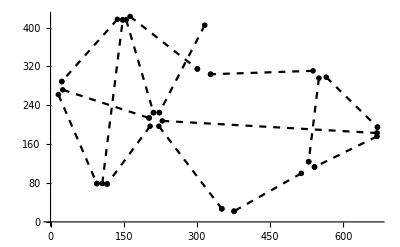

```mathematica
ListLinePlot[edgesEndpointsCoordinates,PlotStyle->Dashed,PlotTheme->"Monochrome"]
```

```mathematica
edgesEndpointsConnections=Fold[Function[ReplaceAll[#1,{a_Integer,b_Integer}/;EuclideanDistance[{a,b},Last[#2]]<20->First[#2]]],edgesEndpointsCoordinates,verticesCoordinates]
```

{{8,10},{7,8},{6,10},{6,9},{5,9},{3,7},{3,4},{1,6},{1,5},{9,1},{5,6},{2,6},{1,4},{3,8},{6,7}}

```mathematica
positions=Map[Rest,flattening[verticesCoordinates]]
```

{{149.,429.5},{324.,418.5},{551.,309.5},{314.,303.5},{11.,275.5},{214.914,210.534},{682.,182.5},{527.,109.5},{104.,64.5},{362.,13.5}}

```mathematica
weighted=Round[Map[Function[distance [First[edgesEndpointsConnections[[#]]],Last[edgesEndpointsConnections[[#]]]]],Range[Length[edgesEndpointsConnections]]]]
```

{191,171,246,183,231,182,237,229,207,368,214,235,208,201,468}

```mathematica
graph=Graph[Range[Length[verticesCoordinates]],Apply[UndirectedEdge,edgesEndpointsConnections,{1}],VertexCoordinates->Values[verticesCoordinates],EdgeWeight->weighted,EdgeLabels->"EdgeWeight",GraphStyle->"SmallNetwork"]
```

-Graphics-

## US Network

```mathematica
image=Image[GeoGraphPlot[{Entity["City", {"Miami", "Florida", "UnitedStates"}]<->Entity["City", {"Jacksonville", "Florida", "UnitedStates"}],
Entity["City", {"SanFrancisco", "California", "UnitedStates"}]<->Entity["City", {"LosAngeles", "California", "UnitedStates"}],Entity["City", {"Dallas", "Texas", "UnitedStates"}]<->Entity["City", {"Houston", "Texas", "UnitedStates"}],
Entity["City", {"SanFrancisco", "California", "UnitedStates"}]<->Entity["City", {"Seattle", "Washington", "UnitedStates"}],Entity["City", {"Helena", "Montana", "UnitedStates"}]<->Entity["City", {"Seattle", "Washington", "UnitedStates"}],Entity["City", {"Jacksonville", "Florida", "UnitedStates"}]<->Entity["City", {"Atlanta", "Georgia", "UnitedStates"}],Entity["City", {"Dallas", "Texas", "UnitedStates"}]<->Entity["City", {"Atlanta", "Georgia", "UnitedStates"}],Entity["City", {"Washington", "DistrictOfColumbia", "UnitedStates"}]<->Entity["City", {"Atlanta", "Georgia", "UnitedStates"}],Entity["City", {"Washington", "DistrictOfColumbia", "UnitedStates"}]<->Entity["City", {"Boston", "Massachusetts", "UnitedStates"}],Entity["City", {"Washington", "DistrictOfColumbia", "UnitedStates"}]<->Entity["City", {"Jacksonville", "Florida", "UnitedStates"}],Entity["City", {"SaintLouis", "Missouri", "UnitedStates"}]<->Entity["City", {"Atlanta", "Georgia", "UnitedStates"}],Entity["City", {"SaintLouis", "Missouri", "UnitedStates"}]<->Entity["City", {"Chicago", "Illinois", "UnitedStates"}],Entity["City", {"Dallas", "Texas", "UnitedStates"}]<->Entity["City", {"Albuquerque", "NewMexico", "UnitedStates"}],
Entity["City", {"Dallas", "Texas", "UnitedStates"}]<->Entity["City", {"Denver", "Colorado", "UnitedStates"}],Entity["City", {"LosAngeles", "California", "UnitedStates"}]<->Entity["City", {"Albuquerque", "NewMexico", "UnitedStates"}],Entity["City", {"Houston", "Texas", "UnitedStates"}]<->Entity["City", {"NewOrleans", "Louisiana", "UnitedStates"}],Entity["City", {"Jacksonville", "Florida", "UnitedStates"}]<->Entity["City", {"NewOrleans", "Louisiana", "UnitedStates"}],Entity["City", {"Minneapolis", "Minnesota", "UnitedStates"}]<->Entity["City", {"Chicago", "Illinois", "UnitedStates"}],Entity["City", {"KansasCity", "Missouri", "UnitedStates"}]<->Entity["City", {"Minneapolis", "Minnesota", "UnitedStates"}],Entity["City", {"KansasCity", "Missouri", "UnitedStates"}]<->Entity["City", {"Dallas", "Texas", "UnitedStates"}],
Entity["City", {"KansasCity", "Missouri", "UnitedStates"}]<->Entity["City", {"Albuquerque", "NewMexico", "UnitedStates"}],Entity["City", {"KansasCity", "Missouri", "UnitedStates"}]<->Entity["City", {"SaintLouis", "Missouri", "UnitedStates"}],Entity["City", {"Denver", "Colorado", "UnitedStates"}]<->Entity["City", {"Albuquerque", "NewMexico", "UnitedStates"}],Entity["City", {"Denver", "Colorado", "UnitedStates"}]<->Entity["City", {"SaltLakeCity", "Utah", "UnitedStates"}],Entity["City", {"SaintLouis", "Missouri", "UnitedStates"}]<->Entity["City", {"Indianapolis", "Indiana", "UnitedStates"}],Entity["City", {"Washington", "DistrictOfColumbia", "UnitedStates"}]<->Entity["City", {"Chicago", "Illinois", "UnitedStates"}],Entity["City", {"Minneapolis", "Minnesota", "UnitedStates"}]<->Entity["City", {"Helena", "Montana", "UnitedStates"}],Entity["City", {"SaltLakeCity", "Utah", "UnitedStates"}]<->Entity["City", {"LosAngeles", "California", "UnitedStates"}],Entity["City", {"SaltLakeCity", "Utah", "UnitedStates"}]<->Entity["City", {"Tucson", "Arizona", "UnitedStates"}],Entity["City", {"SaltLakeCity", "Utah", "UnitedStates"}]<->Entity["City", {"Albuquerque", "NewMexico", "UnitedStates"}],Entity["City", {"SanFrancisco", "California", "UnitedStates"}]<->Entity["City", {"Helena", "Montana", "UnitedStates"}],Entity["City", {"KansasCity", "Missouri", "UnitedStates"}]<->Entity["City", {"Helena", "Montana", "UnitedStates"}],Entity["City", {"SaltLakeCity", "Utah", "UnitedStates"}]<->Entity["City", {"Seattle", "Washington", "UnitedStates"}],Entity["City", {"Denver", "Colorado", "UnitedStates"}]<->Entity["City", {"Minneapolis", "Minnesota", "UnitedStates"}],Entity["City", {"LosAngeles", "California", "UnitedStates"}]<->Entity["City", {"Tucson", "Arizona", "UnitedStates"}],Entity["City", {"ElPaso", "Texas", "UnitedStates"}]<->Entity["City", {"Houston", "Texas", "UnitedStates"}],Entity["City", {"ElPaso", "Texas", "UnitedStates"}]<->Entity["City", {"Dallas", "Texas", "UnitedStates"}],Entity["City", {"Indianapolis", "Indiana", "UnitedStates"}]<->Entity["City", {"Atlanta", "Georgia", "UnitedStates"}],Entity["City", {"Indianapolis", "Indiana", "UnitedStates"}]<->Entity["City", {"Boston", "Massachusetts", "UnitedStates"}],Entity["City", {"SaintLouis", "Missouri", "UnitedStates"}]<->Entity["City", {"NewOrleans", "Louisiana", "UnitedStates"}],Entity["City", {"ElPaso", "Texas", "UnitedStates"}]<->Entity["City", {"Tucson", "Arizona", "UnitedStates"}]},ImageSize->Large]]
```

-Graphics-

```mathematica
graphImage=ImageAdjust[ColorQuantize[ColorSeparate[image,"RGB"][[2]],2,Dithering->False]]
```

-Graphics-

```mathematica
Grid[{{"image","graphImage (extracted)",""},{image,graphImage}},Frame->All]
```

image | graphImage (extracted) | 
-Graphics- | -Graphics- |

```mathematica
binarizedImage=Binarize[graphImage];
detectedVertices=SelectComponents[binarizedImage,"Count",Function[5<#<100]];
verticesCoordinates=ComponentMeasurements[detectedVertices,"Centroid"];
detectedEdges=DeleteSmallComponents[ImageSubtract[Thinning[ColorNegate[binarizedImage]],Dilation[detectedVertices,10]],2];
separatedEdges=Map[Composition[Binarize,Image],Values[ComponentMeasurements[detectedEdges,"Mask"]]];
detectedCrosses=Select[separatedEdges,Function[ImageMeasurements[MorphologicalBranchPoints[#],"Total"]>1]];
nonOverlapEdgesEndpointsCoordinates=Map[Function[PixelValuePositions[#,1]],MorphologicalTransform[Complement[separatedEdges,detectedCrosses],"EndPoints"]];
separatedCrossesAtCenter=MapThread[ImageSubtract,{detectedCrosses,Map[Function[Dilation[MorphologicalBranchPoints[#],3]],detectedCrosses]}];
separatedCrosses=Map[Function[Map[Composition[Binarize,Image],Values[ComponentMeasurements[#,"Mask"]]]],separatedCrossesAtCenter];
crossesCenterPointsCoordinates=MapThread[Function[Nearest[PixelValuePositions[MorphologicalTransform[#1,"EndPoints"],1],Mean[PixelValuePositions[MorphologicalBranchPoints[#2],1]],4]],{separatedCrossesAtCenter,detectedCrosses}];
separatedCrossesEndpointsCoordinates=Table[Map[Function[PixelValuePositions[#,1]],Map[Function[MorphologicalTransform[#,"EndPoints"]],i]],{i,separatedCrosses}];
arrangingFunction[a_]:=Module[{b,f},b=Subsets[Range[Length[a]],{2}];
f=Function[Nearest[#->Range[Length[#]]]][Map[Function[Apply[EuclideanDistance,a[[#]]]],b]];
b[[f[3.14,Length[a]/2]]]];
unarrangedCrossesEndpointsCoordinates=MapThread[Function[{a,b},Catenate[MapThread[Complement,{Catenate[Map[Function[Select[a,MemberQ[#]]],b]],Map[List,b]}]]],{separatedCrossesEndpointsCoordinates,crossesCenterPointsCoordinates}];
crossesEndpointsConnections=MapThread[Function[arrangingFunction[Table[Apply[ArcTan,PixelValuePositions[Image[MorphologicalComponents[#1]],PixelValue[Image[MorphologicalComponents[#1]],i]];
N[Mean[Select[PixelValuePositions[Image[MorphologicalComponents[#1]],PixelValue[Image[MorphologicalComponents[#1]],i]],Function[Norm[#-i]<20]]]]-i],{i,#2}]]],{separatedCrossesAtCenter,unarrangedCrossesEndpointsCoordinates}];
crossesEndpointsCoordinates=MapThread[Function[Map[Function[i,Part[#1,i]],#2]],{unarrangedCrossesEndpointsCoordinates,crossesEndpointsConnections}];
edgesEndpointsCoordinates=Fold[Function[Join[#1,#2]],nonOverlapEdgesEndpointsCoordinates,crossesEndpointsCoordinates];
edgesEndpointsConnections=Fold[Function[ReplaceAll[#1,{a_Integer,b_Integer}/;EuclideanDistance[{a,b},Last[#2]]<20->First[#2]]],edgesEndpointsCoordinates,verticesCoordinates];
flattening[assoc_]:=Map[Flatten,Apply[List,Normal[assoc],{1}]];
positions=Map[Rest,flattening[verticesCoordinates]];
distance[a_,b_]:=EuclideanDistance[positions[[a]],positions[[b]]];
weighted=Round[Map[Function[distance [First[edgesEndpointsConnections[[#]]],Last[edgesEndpointsConnections[[#]]]]],Range[Length[edgesEndpointsConnections]]]];
graph=Graph[Range[Length[verticesCoordinates]],Apply[UndirectedEdge,edgesEndpointsConnections,{1}],VertexCoordinates->Values[verticesCoordinates],EdgeWeight->weighted,GraphStyle->"SimpleLink",ImageSize->Large]
```

-Graphics-

```mathematica
HighlightGraph[graph,PathGraph[FindShortestPath[graph,RandomInteger[{1,Length[verticesCoordinates]}],RandomInteger[{1,Length[verticesCoordinates]}],Method->"Dijkstra"]]]
```

-Graphics-

```mathematica
HighlightGraph[graph,FindSpanningTree[graph]]
```

-Graphics-

```mathematica
route=First[FindPostmanTour[graph]]
```

{1<->7,7<->13,13<->16,16<->18,18<->21,21<->20,20<->21,21<->17,17<->14,14<->11,11<->17,17<->18,18<->16,16<->6,6<->14,14<->13,13<->6,6<->14,14<->10,10<->17,17<->15,15<->19,19<->22,22<->19,19<->20,20<->12,12<->11,11<->3,3<->10,10<->6,6<->1,1<->7,7<->2,2<->11,11<->12,12<->15,15<->19,19<->8,8<->15,15<->9,9<->12,12<->5,5<->12,12<->9,9<->4,4<->8,8<->5,5<->3,3<->2,2<->1}

```mathematica
DirectedGraph[route]
```

-Graphics-